# Hopf Bifurcation in Fast-Slow Van der Pol System

## The Van Der Pol System

```mathematica
f1[x1_,x2_,λ_]:=(x2 + (x1 - (x1^3)/3)) /ϵ;
f2[x1_,x2_,λ_]:=-x1 + λ;
fλ[x1_,x2_,λ_]:= r;
```

```mathematica
ϵ=.1;
r=.001;
```

```mathematica
Clear[x1,x2,t,λ]
```

```mathematica
solution1 =NDSolve[{
x1'[t]==f1[x1[t],x2[t],λ[t]],
x2'[t]==f2[x1[t],x2[t],λ[t]],
λ'[t]==fλ[x1[t],x2[t],λ[t]],
x1[0]==0,
x2[0]==0,
λ[0]==-1},{x1,x2,λ},{t,0,200},MaxSteps->200000]
```

{{x1→InterpolatingFunction[{{0., 200.}}, <>],x2→InterpolatingFunction[{{0., 200.}}, <>],λ→InterpolatingFunction[{{0., 200.}}, <>]}}

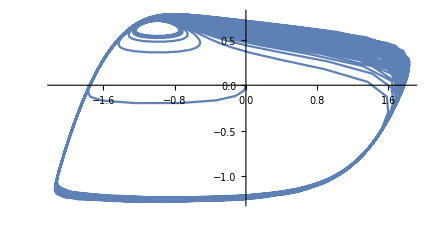

```mathematica
ParametricPlot[Evaluate[{x1[t],x2[t]}/.solution1],{t,0,200},PlotRange->All]
```

```mathematica
solution2 =NDSolve[{
x1'[t]==f1[x1[t],x2[t],0],
x2'[t]==f2[x1[t],x2[t],.98],
x1[0]==0,
x2[0]==0},{x1,x2},{t,0,200},MaxSteps->200000]
```

{{x1→InterpolatingFunction[{{0., 200.}}, <>],x2→InterpolatingFunction[{{0., 200.}}, <>]}}

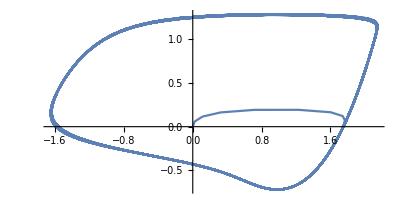

```mathematica
ParametricPlot[Evaluate[{x1[t],x2[t]}/.solution2],{t,0,200},PlotRange->All]
```

## Another version of forcing the Van Der Pol system

```mathematica
Clear[λ]
```

```mathematica
f1[x1_,x2_,λ_]:=(x2 +λ+ x1 - (x1^3)/3) /ϵ;
f2[x1_,x2_,λ_]:=-x1-1.1;
fλ[x1_,x2_,λ_]:= r;
```

```mathematica
ϵ=.1;
r=2.2;
solution1 =NDSolve[{
x1'[t]==f1[x1[t],x2[t],λ[t]],
x2'[t]==f2[x1[t],x2[t],λ[t]],
λ'[t]==fλ[x1[t],x2[t],λ[t]],
x1[0]==-1,
x2[0]==.66,
λ[0]==0},{x1,x2,λ},{t,0,200},MaxSteps->200000]
ParametricPlot[Evaluate[{x1[t],x2[t]}/.solution1],{t,0,200},PlotRange->All];
```

{{x1→InterpolatingFunction[{{0., 200.}}, <>],x2→InterpolatingFunction[{{0., 200.}}, <>],λ→InterpolatingFunction[{{0., 200.}}, <>]}}

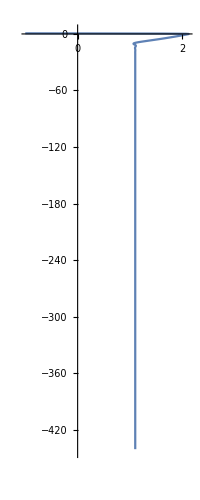

```mathematica
ParametricPlot[Evaluate[{x1[t],x2[t]}/.solution1],{t,0,200},PlotRange->All]
```

## Reduced System

```mathematica
ϵ = .017;
```

```mathematica
λ = 0;
```

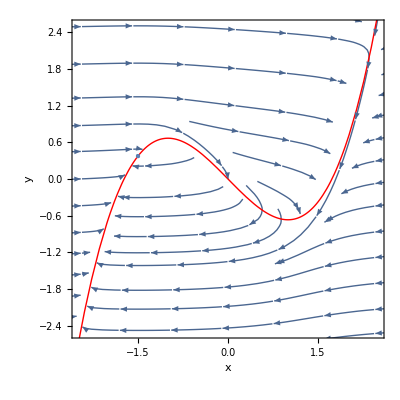

```mathematica
p1=StreamPlot[{(y + (x - (x^3)/3))/ϵ,-x-1.5},{x,-5,5},{y,-5,5}];
p2=Plot[-(x - (x^3)/3),{x,-3,3},PlotStyle->{Thick,Red},PlotRange->{-3,3}];
 p3=ListPlot[{{-1.5,-((-1.5) - ((-1.5)^3)/3)}},PlotStyle->PointSize[Large]];
Show[p1,p2,p3,PlotRange->{{-2.5,2.5},{-2.5,2.5}}, FrameLabel->{"x","y"},LabelStyle->Directive[16]]
```

```mathematica
plot1 = ParametricPlot3D[{x,-λλ- (x - (x^3)/3),λλ},{x,-3,3},{λλ,-3,5},PlotRange->{{-3,3},{-10,4},{-2,5}},PlotStyle->Directive[Opacity[.4],Blue],Mesh->None,AxesLabel->{"x","y","λ"}];
plot2=ParametricPlot3D[{-1.5,-λλ-((-1.5) - ((-1.5)^3)/3),λλ},{λλ,-3,5},PlotRange->{{-3,3},{-10,4},{-2,5}},PlotStyle->{Red,Thick}];
plot3=ParametricPlot3D[{-1,-λλ-((-1) - ((-1)^3)/3),λλ},{λλ,-3,5},PlotRange->{{-3,3},{-10,4},{-2,5}},PlotStyle->{Red,Thick,Dashed}];Show[plot1, plot2,plot3]
```

-Graphics3D-

## Equilibrium Analysis

```mathematica
J = {{(1-x^2)/e,1/e},{-1,0}}
```

{{(1-x^2)/e,1/e},{-1,0}}

```mathematica
f[x_,e_]=Eigenvalues[J]
```

{(1-x^2-√(1-4 e-2 x^2+x^4))/(2 e),(1-x^2+√(1-4 e-2 x^2+x^4))/(2 e)}

## Plots

```mathematica
Clear[x,y,L,t,ϵ]
r = .503;
ϵ = .02;
sol = NDSolve[{
x'[t]==(y[t] + L[t]+ (x[t]- (x[t]^3)/3))/ϵ,
y'[t]==-x[t] - 1.5,
L'[t]==r,
x[0]==-1.5,y[0]==0,L[0]==0},{x,y,L},{t,0,20}];
p6 = ParametricPlot3D[{x[t],y[t],L[t]}/.sol,{t,0,20},PlotRange->{{-3,3},{-10,4},{-2,5}},PlotStyle->{Green,Thickness[.005]}];

Clear[x,y,L,t,ϵ]
r = .1;
ϵ = .02;
sol = NDSolve[{
x'[t]==(y[t] + L[t]+ (x[t]- (x[t]^3)/3))/ϵ,
y'[t]==-x[t] - 1.5,
L'[t]==r,
x[0]==-1.5,y[0]==0,L[0]==0},{x,y,L},{t,0,40}];
p7 = ParametricPlot3D[{x[t],y[t],L[t]}/.sol,{t,0,50},PlotRange->{{-3,3},{-10,4},{-2,5}},PlotStyle->{Blue,Thickness[.005]}];

Clear[x,y,L,t,ϵ]
r = .5025;
ϵ = .02;
sol = NDSolve[{
x'[t]==(y[t] + L[t]+ (x[t]- (x[t]^3)/3))/ϵ,
y'[t]==-x[t] - 1.5,
L'[t]==r,
x[0]==-1.5,y[0]==0,L[0]==0},{x,y,L},{t,0,20}];
p8 = ParametricPlot3D[{x[t],y[t],L[t]}/.sol,{t,0,20},PlotRange->{{-3,3},{-10,4},{-2,5}},PlotStyle->{Orange,Thickness[.005]}];
```

```mathematica
Show[plot1,plot2,plot3,p6,p7,p8, PlotRange->{{-3,3},{-6,3},{-2,5}},AxesLabel->{"x","y","λ"},LabelStyle->Directive[16]]
```

-Graphics3D-

## More trajectories

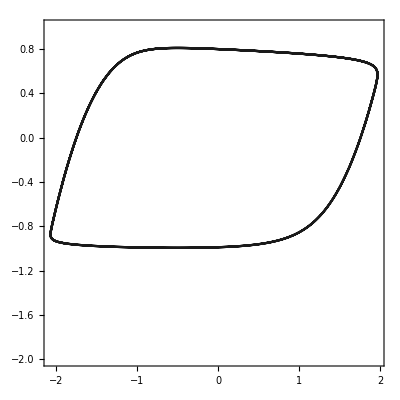

```mathematica
Clear[x,y,L,t,ϵ]
r = 1.0;
ϵ = .05;
sol = NDSolve[{
x'[t]==(y[t] + (x[t]- (x[t]^3)/3))/ϵ,
y'[t]==-x[t] - 1.5 + r,
x[0]==-1.5,y[0]==0},{x,y},{t,0,20}];
pp1 = ParametricPlot[{x[t],y[t]}/.sol,{t,10,20},PlotRange->{All,{-2,1}},PlotStyle->GrayLevel[.1],Frame->True, AspectRatio->1]
```

General::prng: Value of option PlotRange -> {All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

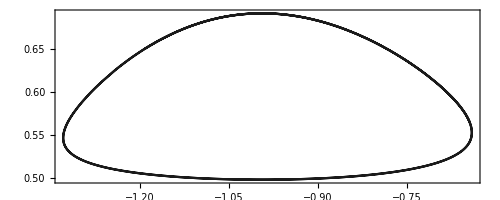

```mathematica
Clear[x,y,L,t,ϵ]
r = .5061;
ϵ = .05;
sol = NDSolve[{
x'[t]==(y[t] + (x[t]- (x[t]^3)/3))/ϵ,
y'[t]==-x[t] - 1.5 + r,
x[0]==-1.5,y[0]==0},{x,y},{t,0,20}];
pp2 = ParametricPlot[{x[t],y[t]}/.sol,{t,15,20},PlotRange->{All},PlotStyle->GrayLevel[.1],Frame->True]
```

General::prng: Value of option PlotRange -> {All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

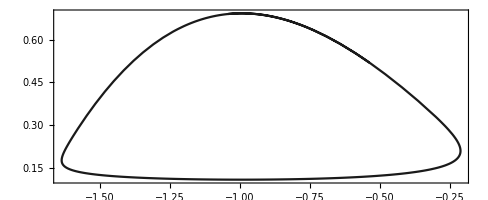

```mathematica
Clear[x,y,L,t,ϵ]
r = .50650917;
ϵ = .05;
sol = NDSolve[{
x'[t]==(y[t] + (x[t]- (x[t]^3)/3))/ϵ,
y'[t]==-x[t] - 1.5 + r,
x[0]==-1.5,y[0]==0},{x,y},{t,0,100}];
pp3 = ParametricPlot[{x[t],y[t]}/.sol,{t,90,94},PlotRange->{All},PlotStyle->GrayLevel[.1],Frame->True]
```

General::prng: Value of option PlotRange -> {All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

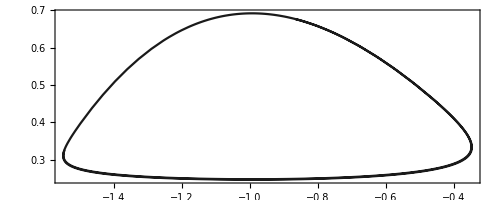

```mathematica
Clear[x,y,L,t,ϵ]
r = .506508;
ϵ = .05;
sol = NDSolve[{
x'[t]==(y[t] + (x[t]- (x[t]^3)/3))/ϵ,
y'[t]==-x[t] - 1.5 + r,
x[0]==-1.5,y[0]==0},{x,y},{t,0,100}];
pp7 = ParametricPlot[{x[t],y[t]}/.sol,{t,90,94},PlotRange->{All},PlotStyle->GrayLevel[.1],Frame->True]
```

General::prng: Value of option PlotRange -> {All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

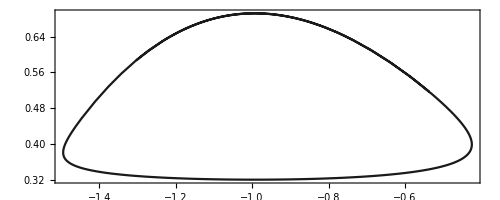

```mathematica
Clear[x,y,L,t,ϵ]
r = .506503;
ϵ = .05;
sol = NDSolve[{
x'[t]==(y[t] + (x[t]- (x[t]^3)/3))/ϵ,
y'[t]==-x[t] - 1.5 + r,
x[0]==-1.5,y[0]==0},{x,y},{t,0,100}];
pp8 = ParametricPlot[{x[t],y[t]}/.sol,{t,90,94},PlotRange->{All},PlotStyle->GrayLevel[.1],Frame->True]
```

General::prng: Value of option PlotRange -> {All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

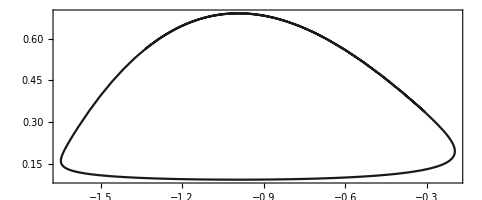

```mathematica
Clear[x,y,L,t,ϵ]
r = .50650919;
ϵ = .05;
sol = NDSolve[{
x'[t]==(y[t] + (x[t]- (x[t]^3)/3))/ϵ,
y'[t]==-x[t] - 1.5 + r,
x[0]==-1.5,y[0]==0},{x,y},{t,0,20}];
pp4 = ParametricPlot[{x[t],y[t]}/.sol,{t,14,19},PlotRange->{All},PlotStyle->GrayLevel[.1],Frame->True]
```

```mathematica
Clear[x,y,L,t,ϵ]
r = .5065099;
ϵ = .05;
sol = NDSolve[{
x'[t]==(y[t] + (x[t]- (x[t]^3)/3))/ϵ,
y'[t]==-x[t] - 1.5 + r,
x[0]==-1.5,y[0]==0},{x,y},{t,0,20}];
pp5 = ParametricPlot[{x[t],y[t]}/.sol,{t,14,19},PlotRange->{All},PlotStyle->GrayLevel[.1],Frame->True];
```

General::prng: Value of option PlotRange -> {All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

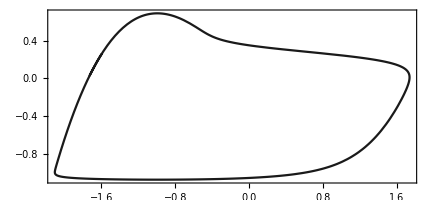

```mathematica
Clear[x,y,L,t,ϵ]
r = .50653;
ϵ = .05;
sol = NDSolve[{
x'[t]==(y[t] + (x[t]- (x[t]^3)/3))/ϵ,
y'[t]==-x[t] - 1.5 + r,
x[0]==-1.5,y[0]==0},{x,y},{t,0,20}];
pp6 = ParametricPlot[{x[t],y[t]}/.sol,{t,14,19},PlotRange->{All},PlotStyle->GrayLevel[.1],Frame->True]
```

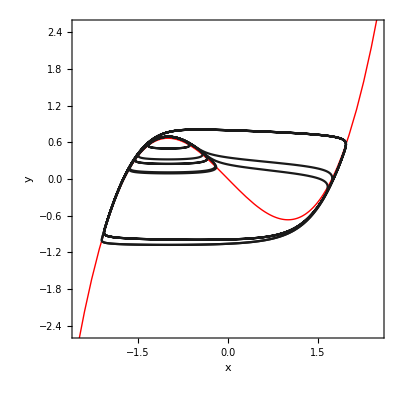

-Graphics-

```mathematica
Show[p2,pp1,pp2,pp3,pp4,pp5,pp6,pp7,pp8, PlotRange->{{-2.5,2.5},{-2.5,2.5}}, Frame->True,AspectRatio->1, FrameLabel->{"x","y"} ,LabelStyle->Directive[16]]
```